```mathematica
<<xSSA.m
```

xSSAlite 1.2.01 (1-March-2011) loaded Tue-8-Mar-2011-09:04:51 using Mathematica 8.0 for Linux x86 (64-bit) (November 7, 2010)(8.0.0)

## Basic Enzymatic Interaction

```mathematica
M1={{Overscript[S⇄P, ℰ],k1,k2,k3,k4}};
r={k1->0.2, k2-> 0.01, k3-> 0.5, k4-> 0}; 
ic={S-> 5, P-> 0, ℰ-> 100,S⋄ℰ-> 0};
```

```mathematica
sim = SSA[M1,50, ic, r]
```

a0 = 0 at t=1.9549

xSSA Exit. 12 steps.  10 points sampled.  0.00371 seconds.

{P→{{0,0},{0.02172,0},{0.0405982,0},{0.0413169,0},{0.0548699,0},{0.0549754,0},{0.558392,1},{0.591687,2},{0.684123,3},{0.814545,4},{1.9549,5}},S→{{0,5},{0.02172,4},{0.0405982,3},{0.0413169,2},{0.0548699,1},{0.0549754,0},{0.558392,0},{0.591687,0},{0.684123,0},{0.814545,0},{1.9549,0}},ℰ→{{0,100},{0.02172,99},{0.0405982,98},{0.0413169,97},{0.0548699,96},{0.0549754,95},{0.558392,96},{0.591687,97},{0.684123,98},{0.814545,99},{1.9549,100}},S⋄ℰ→{{0,0},{0.02172,1},{0.0405982,2},{0.0413169,3},{0.0548699,4},{0.0549754,5},{0.558392,4},{0.591687,3},{0.684123,2},{0.814545,1},{1.9549,0}}}

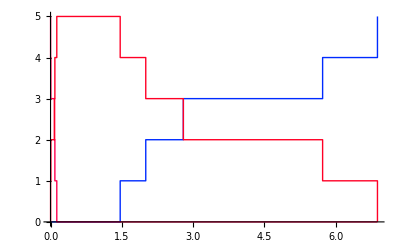

```mathematica
SSAPlot[sim]
```

#### Tabular Output

```mathematica
SSA[M1,50, ic, r, "Mode"-> "Table"]//TableForm
```

a0 = 0 at t=5.0097

xSSA Exit. 12 steps.  10 points sampled.  0.00388 seconds.

time | P | S | ℰ | S⋄ℰ
0 | 0 | 5 | 100 | 0
0.0179495 | 0 | 4 | 99 | 1
0.0282324 | 0 | 3 | 98 | 2
0.0378507 | 0 | 2 | 97 | 3
0.063819 | 0 | 1 | 96 | 4
0.0730422 | 1 | 1 | 97 | 3
0.0991264 | 1 | 0 | 96 | 4
1.18258 | 2 | 0 | 97 | 3
1.87099 | 3 | 0 | 98 | 2
2.18385 | 4 | 0 | 99 | 1
5.0097 | 5 | 0 | 100 | 0

#### Interpolating Function

```mathematica
SSA[M1,50, ic, r, "Mode"-> "Interpolation"]
```

a0 = 0 at t=2.24325

xSSA Exit. 12 steps.  10 points sampled.  0.00457 seconds.

{P→InterpolatingFunction[{{0.,2.24325}},<>],S→InterpolatingFunction[{{0.,0.174002}},<>],ℰ→InterpolatingFunction[{{0.,2.24325}},<>],S⋄ℰ→InterpolatingFunction[{{0.,2.24325}},<>]}

#### Table of specific variables

```mathematica
SSA[M1,50, ic, r,  "Mode"-> "Variables", "Variables"-> {S,P}]
```

a0 = 0 at t=5.2869

xSSA Exit. 12 steps.  10 points sampled.  0.00429 seconds.

{{t,S,S ⋄ ℰ,P,P},{0,5,0,0,0},{0.00975194,4,1,0,0},{0.0322593,3,2,0,0},{0.0437847,2,3,0,0},{0.0522741,1,4,0,0},{0.177023,0,5,0,0},{0.82707,0,4,1,1},{1.08232,0,3,2,2},{4.02003,0,2,3,3},{5.16929,0,1,4,4},{5.2869,0,0,5,5},{5.2869,0,0,5,5}}

## Stochastic Ring Oscillator

```mathematica
rings={{Underoverscript[X⇄XP, ZPP, Z],a,d,k,0, a,d,k, 0},
{Underoverscript[XP⇄XPP, ZPP, Z],a,d,k,0,a,d,k,0},{Underoverscript[Y⇄YP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[YP⇄YPP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[Z⇄ZP, YPP, Y],a,d,k,0,a,d,k,0},{Underoverscript[ZP⇄ZPP, YPP, Y],a,d,k,0,a,d,k,0}};
r={a-> 1, d-> 1, k-> 1};
IC={X-> 60, Y-> 40, Z-> 20};
```

```mathematica
sr=SSA[rings,100, IC, r, "Mode"-> "Interpolation"]
```

Warning:  the following variables are missing initial condtions, which are all assumed to be zero: {XP,XPP,YP,YPP,ZP,ZPP,X⋄Z,XP⋄Z,XP⋄ZPP,XPP⋄ZPP,Y⋄X,YP⋄X,YP⋄XPP,YPP⋄XPP,Z⋄Y,ZP⋄Y,ZP⋄YPP,ZPP⋄YPP}

xSSA Exit. 16614 steps.  16613 points sampled.  5.57881 seconds.

{X→InterpolatingFunction[{{0.,100.001}},<>],XP→InterpolatingFunction[{{0.,99.8687}},<>],XPP→InterpolatingFunction[{{0.,99.9892}},<>],Y→InterpolatingFunction[{{0.,99.9849}},<>],YP→InterpolatingFunction[{{0.,100.001}},<>],YPP→InterpolatingFunction[{{0.,99.9814}},<>],Z→InterpolatingFunction[{{0.,96.5601}},<>],ZP→InterpolatingFunction[{{0.,99.9814}},<>],ZPP→InterpolatingFunction[{{0.,99.9563}},<>],X⋄Z→InterpolatingFunction[{{0.,94.1981}},<>],XP⋄Z→InterpolatingFunction[{{0.,94.7803}},<>],XP⋄ZPP→InterpolatingFunction[{{0.,99.8687}},<>],XPP⋄ZPP→InterpolatingFunction[{{0.,99.9563}},<>],Y⋄X→InterpolatingFunction[{{0.,99.9849}},<>],YP⋄X→InterpolatingFunction[{{0.,100.001}},<>],YP⋄XPP→InterpolatingFunction[{{0.,99.9892}},<>],YPP⋄XPP→InterpolatingFunction[{{0.,99.9776}},<>],Z⋄Y→InterpolatingFunction[{{0.,96.6993}},<>],ZP⋄Y→InterpolatingFunction[{{0.,99.6795}},<>],ZP⋄YPP→InterpolatingFunction[{{0.,99.9814}},<>],ZPP⋄YPP→InterpolatingFunction[{{0.,99.89}},<>]}

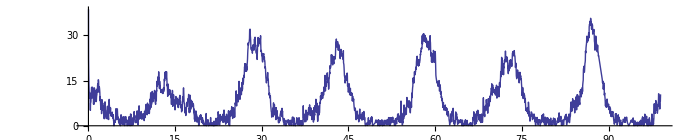

```mathematica
sp=Plot[X[t]/.sr, {t, 0, 99}, ImageSize->700, AspectRatio-> .2]
```

### Compare the single run with a single xlr8r run

```mathematica
<<xlr8r.m
```

xlr8r 0.80 (22 Feb 2011) loaded 08 March 2011 at 09:05 GMT-07:60 using Mathematica 8.0 for Linux x86 (64-bit) (November 7, 2010) (Version 8., Release 0) (MathSBML 2.10.1 [11-Feb-2011])
GNU Lesser General Public License (LGPL) Terms Apply.

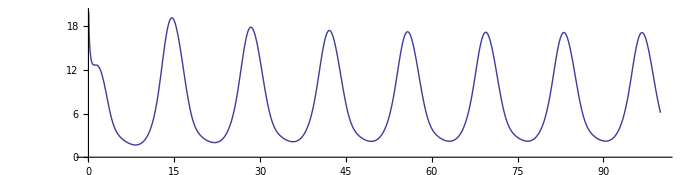

```mathematica
xr=run[rings, initialConditions-> IC, rates-> r];
xp=Plot[X[t]/.xr, {t, 0, 100}, PlotRange-> {0, 20}, ImageSize-> 700, AspectRatio-> .25]
```

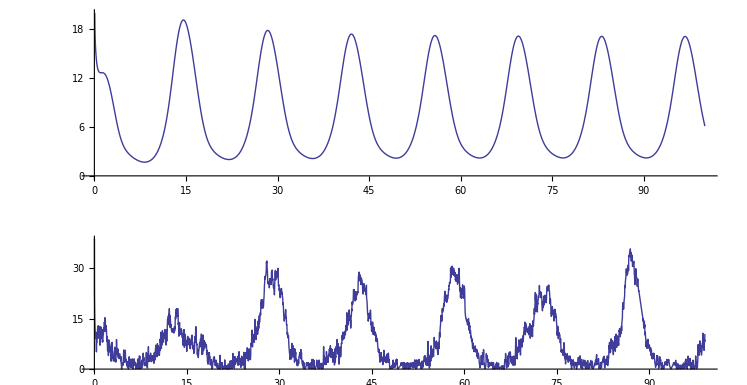

```mathematica
GraphicsColumn[{xp,sp}]
```

## Cellzilla2D Stochastic Example with interacting Ring Oscillators

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.1.α.23 24-Feb-2011) loaded Tue 8 Mar 2011 10:15:44 using xlr8r 0.80 (22 Feb 2011) and xSSA 1.2.01 (1-March-2011)

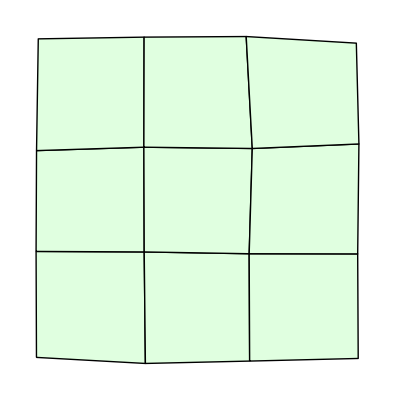

```mathematica
tissue=RandomizeTemplate[TemplateRectangular[3,3], .05];
ShowTissue[tissue]
```

```mathematica
n=NTissueCells[tissue];
rings={{Underoverscript[X⇄XP, ZPP, Z],a,d,k,0, a,d,k, 0},
{Underoverscript[XP⇄XPP, ZPP, Z],a,d,k,0,a,d,k,0},{Underoverscript[Y⇄YP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[YP⇄YPP, XPP, X],a,d,k,0,a,d,k,0},{Underoverscript[Z⇄ZP, YPP, Y],a,d,k,0,a,d,k,0},{Underoverscript[ZP⇄ZPP, YPP, Y],a,d,k,0,a,d,k,0}};
r={a-> 1, d-> 1, k-> 1};
```

```mathematica
rx:= RandomInteger[{50,70}];
ry:=RandomInteger[{30,50}];
rz:=RandomInteger[{10,30}];
```

```mathematica
icr[i_]:= {X[i]-> rx, Y[i]-> ry, Z[i]-> rz};
```

```mathematica
icr[1]
```

{X[1]→50,Y[1]→39,Z[1]→21}

```mathematica
myic=Sort[Flatten[icr/@Range[n]]]
```

{X[1]→54,X[2]→53,X[3]→66,X[4]→68,X[5]→54,X[6]→55,X[7]→61,X[8]→59,X[9]→62,Y[1]→38,Y[2]→44,Y[3]→45,Y[4]→46,Y[5]→33,Y[6]→35,Y[7]→35,Y[8]→46,Y[9]→38,Z[1]→12,Z[2]→19,Z[3]→23,Z[4]→19,Z[5]→12,Z[6]→14,Z[7]→18,Z[8]→30,Z[9]→10}

```mathematica
bignet=SSANetwork[rings, {{X, DX}}, tissue];
```

9 Cells.

48 internal reactions in each cell.

432 intracellular reactions.

24 diffusion reactions.

456 total reactions.

```mathematica
czsim=SSA[bignet, 50, myic, Append[r, DX-> .1], "Mode"-> "Interpolation"]
```

Warning:  the following variables are missing initial condtions, which are all assumed to be zero: {XP[1],XP[2],XP[3],XP[4],XP[5],XP[6],XP[7],XP[8],XP[9],XPP[1],XPP[2],XPP[3],XPP[4],XPP[5],XPP[6],XPP[7],XPP[8],XPP[9],YP[1],YP[2],YP[3],YP[4],YP[5],YP[6],YP[7],YP[8],YP[9],YPP[1],YPP[2],YPP[3],YPP[4],YPP[5],YPP[6],YPP[7],YPP[8],YPP[9],ZP[1],ZP[2],ZP[3],ZP[4],ZP[5],ZP[6],ZP[7],ZP[8],ZP[9],ZPP[1],ZPP[2],ZPP[3],ZPP[4],ZPP[5],ZPP[6],ZPP[7],ZPP[8],ZPP[9],(X⋄Z)[1],(X⋄Z)[2],(X⋄Z)[3],(X⋄Z)[4],(X⋄Z)[5],(X⋄Z)[6],(X⋄Z)[7],(X⋄Z)[8],(X⋄Z)[9],(XP⋄Z)[1],(XP⋄Z)[2],(XP⋄Z)[3],(XP⋄Z)[4],(XP⋄Z)[5],(XP⋄Z)[6],(XP⋄Z)[7],(XP⋄Z)[8],(XP⋄Z)[9],(XP⋄ZPP)[1],(XP⋄ZPP)[2],(XP⋄ZPP)[3],(XP⋄ZPP)[4],(XP⋄ZPP)[5],(XP⋄ZPP)[6],(XP⋄ZPP)[7],(XP⋄ZPP)[8],(XP⋄ZPP)[9],(XPP⋄ZPP)[1],(XPP⋄ZPP)[2],(XPP⋄ZPP)[3],(XPP⋄ZPP)[4],(XPP⋄ZPP)[5],(XPP⋄ZPP)[6],(XPP⋄ZPP)[7],(XPP⋄ZPP)[8],(XPP⋄ZPP)[9],(Y⋄X)[1],(Y⋄X)[2],(Y⋄X)[3],(Y⋄X)[4],(Y⋄X)[5],(Y⋄X)[6],(Y⋄X)[7],(Y⋄X)[8],(Y⋄X)[9],(YP⋄X)[1],(YP⋄X)[2],(YP⋄X)[3],(YP⋄X)[4],(YP⋄X)[5],(YP⋄X)[6],(YP⋄X)[7],(YP⋄X)[8],(YP⋄X)[9],(YP⋄XPP)[1],(YP⋄XPP)[2],(YP⋄XPP)[3],(YP⋄XPP)[4],(YP⋄XPP)[5],(YP⋄XPP)[6],(YP⋄XPP)[7],(YP⋄XPP)[8],(YP⋄XPP)[9],(YPP⋄XPP)[1],(YPP⋄XPP)[2],(YPP⋄XPP)[3],(YPP⋄XPP)[4],(YPP⋄XPP)[5],(YPP⋄XPP)[6],(YPP⋄XPP)[7],(YPP⋄XPP)[8],(YPP⋄XPP)[9],(Z⋄Y)[1],(Z⋄Y)[2],(Z⋄Y)[3],(Z⋄Y)[4],(Z⋄Y)[5],(Z⋄Y)[6],(Z⋄Y)[7],(Z⋄Y)[8],(Z⋄Y)[9],(ZP⋄Y)[1],(ZP⋄Y)[2],(ZP⋄Y)[3],(ZP⋄Y)[4],(ZP⋄Y)[5],(ZP⋄Y)[6],(ZP⋄Y)[7],(ZP⋄Y)[8],(ZP⋄Y)[9],(ZP⋄YPP)[1],(ZP⋄YPP)[2],(ZP⋄YPP)[3],(ZP⋄YPP)[4],(ZP⋄YPP)[5],(ZP⋄YPP)[6],(ZP⋄YPP)[7],(ZP⋄YPP)[8],(ZP⋄YPP)[9],(ZPP⋄YPP)[1],(ZPP⋄YPP)[2],(ZPP⋄YPP)[3],(ZPP⋄YPP)[4],(ZPP⋄YPP)[5],(ZPP⋄YPP)[6],(ZPP⋄YPP)[7],(ZPP⋄YPP)[8],(ZPP⋄YPP)[9]}

xSSA Exit. 79590 steps.  79589 points sampled.  335.33143 seconds.

{X[1]→InterpolatingFunction[{{0.,49.9965}},<>],X[2]→InterpolatingFunction[{{0.,49.9983}},<>],X[3]→InterpolatingFunction[{{0.,49.9857}},<>],X[4]→InterpolatingFunction[{{0.,49.9978}},<>],X[5]→InterpolatingFunction[{{0.,49.9905}},<>],X[6]→InterpolatingFunction[{{0.,49.9917}},<>],X[7]→InterpolatingFunction[{{0.,49.9968}},<>],X[8]→InterpolatingFunction[{{0.,49.9766}},<>],X[9]→InterpolatingFunction[{{0.,49.9963}},<>],XP[1]→InterpolatingFunction[{{0.,49.8913}},<>],XP[2]→InterpolatingFunction[{{0.,49.9821}},<>],XP[3]→InterpolatingFunction[{{0.,49.9119}},<>],XP[4]→InterpolatingFunction[{{0.,49.9541}},<>],XP[5]→InterpolatingFunction[{{0.,49.989}},<>],XP[6]→InterpolatingFunction[{{0.,49.9811}},<>],XP[7]→InterpolatingFunction[{{0.,49.9773}},<>],XP[8]→InterpolatingFunction[{{0.,49.955}},<>],XP[9]→InterpolatingFunction[{{0.,49.9934}},<>],XPP[1]→InterpolatingFunction[{{0.,49.9961}},<>],XPP[2]→InterpolatingFunction[{{0.,49.995}},<>],XPP[3]→InterpolatingFunction[{{0.,49.9966}},<>],XPP[4]→InterpolatingFunction[{{0.,49.9975}},<>],XPP[5]→InterpolatingFunction[{{0.,49.9425}},<>],XPP[6]→InterpolatingFunction[{{0.,49.9808}},<>],XPP[7]→InterpolatingFunction[{{0.,49.9997}},<>],XPP[8]→InterpolatingFunction[{{0.,49.987}},<>],XPP[9]→InterpolatingFunction[{{0.,49.9568}},<>],Y[1]→InterpolatingFunction[{{0.,49.7838}},<>],Y[2]→InterpolatingFunction[{{0.,49.9983}},<>],Y[3]→InterpolatingFunction[{{0.,49.9547}},<>],Y[4]→InterpolatingFunction[{{0.,49.9655}},<>],Y[5]→InterpolatingFunction[{{0.,49.3912}},<>],Y[6]→InterpolatingFunction[{{0.,49.9917}},<>],Y[7]→InterpolatingFunction[{{0.,49.9931}},<>],Y[8]→InterpolatingFunction[{{0.,50.0006}},<>],Y[9]→InterpolatingFunction[{{0.,49.9874}},<>],YP[1]→InterpolatingFunction[{{0.,49.9896}},<>],YP[2]→InterpolatingFunction[{{0.,49.995}},<>],YP[3]→InterpolatingFunction[{{0.,49.9966}},<>],YP[4]→InterpolatingFunction[{{0.,49.9978}},<>],YP[5]→InterpolatingFunction[{{0.,49.9295}},<>],YP[6]→InterpolatingFunction[{{0.,49.9584}},<>],YP[7]→InterpolatingFunction[{{0.,49.9402}},<>],YP[8]→InterpolatingFunction[{{0.,49.987}},<>],YP[9]→InterpolatingFunction[{{0.,49.9963}},<>],YPP[1]→InterpolatingFunction[{{0.,49.9866}},<>],YPP[2]→InterpolatingFunction[{{0.,49.9877}},<>],YPP[3]→InterpolatingFunction[{{0.,49.9836}},<>],YPP[4]→InterpolatingFunction[{{0.,49.9975}},<>],YPP[5]→InterpolatingFunction[{{0.,49.9905}},<>],YPP[6]→InterpolatingFunction[{{0.,49.9808}},<>],YPP[7]→InterpolatingFunction[{{0.,49.9997}},<>],YPP[8]→InterpolatingFunction[{{0.,49.981}},<>],YPP[9]→InterpolatingFunction[{{0.,49.9409}},<>],Z[1]→InterpolatingFunction[{{0.,49.9965}},<>],Z[2]→InterpolatingFunction[{{0.,49.9821}},<>],Z[3]→InterpolatingFunction[{{0.,49.9857}},<>],Z[4]→InterpolatingFunction[{{0.,49.9876}},<>],Z[5]→InterpolatingFunction[{{0.,49.989}},<>],Z[6]→InterpolatingFunction[{{0.,49.8765}},<>],Z[7]→InterpolatingFunction[{{0.,49.9968}},<>],Z[8]→InterpolatingFunction[{{0.,49.981}},<>],Z[9]→InterpolatingFunction[{{0.,49.9605}},<>],ZP[1]→InterpolatingFunction[{{0.,49.901}},<>],ZP[2]→InterpolatingFunction[{{0.,49.8218}},<>],ZP[3]→InterpolatingFunction[{{0.,49.9174}},<>],ZP[4]→InterpolatingFunction[{{0.,49.933}},<>],ZP[5]→InterpolatingFunction[{{0.,49.9421}},<>],ZP[6]→InterpolatingFunction[{{0.,48.4228}},<>],ZP[7]→InterpolatingFunction[{{0.,48.7592}},<>],ZP[8]→InterpolatingFunction[{{0.,50.0006}},<>],ZP[9]→InterpolatingFunction[{{0.,49.1772}},<>],ZPP[1]→InterpolatingFunction[{{0.,49.8832}},<>],ZPP[2]→InterpolatingFunction[{{0.,48.8722}},<>],ZPP[3]→InterpolatingFunction[{{0.,49.939}},<>],ZPP[4]→InterpolatingFunction[{{0.,49.8419}},<>],ZPP[5]→InterpolatingFunction[{{0.,49.9564}},<>],ZPP[6]→InterpolatingFunction[{{0.,49.9811}},<>],ZPP[7]→InterpolatingFunction[{{0.,49.9773}},<>],ZPP[8]→InterpolatingFunction[{{0.,49.938}},<>],ZPP[9]→InterpolatingFunction[{{0.,49.9934}},<>],(X⋄Z)[1]→InterpolatingFunction[{{0.,49.9965}},<>],(X⋄Z)[2]→InterpolatingFunction[{{0.,49.9821}},<>],(X⋄Z)[3]→InterpolatingFunction[{{0.,49.9857}},<>],(X⋄Z)[4]→InterpolatingFunction[{{0.,49.9351}},<>],(X⋄Z)[5]→InterpolatingFunction[{{0.,49.989}},<>],(X⋄Z)[6]→InterpolatingFunction[{{0.,49.8367}},<>],(X⋄Z)[7]→InterpolatingFunction[{{0.,49.9968}},<>],(X⋄Z)[8]→InterpolatingFunction[{{0.,49.9687}},<>],(X⋄Z)[9]→InterpolatingFunction[{{0.,47.725}},<>],(XP⋄Z)[1]→InterpolatingFunction[{{0.,49.9961}},<>],(XP⋄Z)[2]→InterpolatingFunction[{{0.,49.9646}},<>],(XP⋄Z)[3]→InterpolatingFunction[{{0.,49.8539}},<>],(XP⋄Z)[4]→InterpolatingFunction[{{0.,49.9876}},<>],(XP⋄Z)[5]→InterpolatingFunction[{{0.,49.9867}},<>],(XP⋄Z)[6]→InterpolatingFunction[{{0.,49.8765}},<>],(XP⋄Z)[7]→InterpolatingFunction[{{0.,49.973}},<>],(XP⋄Z)[8]→InterpolatingFunction[{{0.,49.9239}},<>],(XP⋄Z)[9]→InterpolatingFunction[{{0.,49.2591}},<>],(XP⋄ZPP)[1]→InterpolatingFunction[{{0.,49.62}},<>],(XP⋄ZPP)[2]→InterpolatingFunction[{{0.,46.8514}},<>],(XP⋄ZPP)[3]→InterpolatingFunction[{{0.,49.9119}},<>],(XP⋄ZPP)[4]→InterpolatingFunction[{{0.,49.8419}},<>],(XP⋄ZPP)[5]→InterpolatingFunction[{{0.,49.9564}},<>],(XP⋄ZPP)[6]→InterpolatingFunction[{{0.,49.9811}},<>],(XP⋄ZPP)[7]→InterpolatingFunction[{{0.,49.9773}},<>],(XP⋄ZPP)[8]→InterpolatingFunction[{{0.,49.938}},<>],(XP⋄ZPP)[9]→InterpolatingFunction[{{0.,49.9932}},<>],(XPP⋄ZPP)[1]→InterpolatingFunction[{{0.,49.859}},<>],(XPP⋄ZPP)[2]→InterpolatingFunction[{{0.,48.8722}},<>],(XPP⋄ZPP)[3]→InterpolatingFunction[{{0.,49.7868}},<>],(XPP⋄ZPP)[4]→InterpolatingFunction[{{0.,49.5656}},<>],(XPP⋄ZPP)[5]→InterpolatingFunction[{{0.,49.4668}},<>],(XPP⋄ZPP)[6]→InterpolatingFunction[{{0.,49.8378}},<>],(XPP⋄ZPP)[7]→InterpolatingFunction[{{0.,49.7013}},<>],(XPP⋄ZPP)[8]→InterpolatingFunction[{{0.,49.8856}},<>],(XPP⋄ZPP)[9]→InterpolatingFunction[{{0.,49.9934}},<>],(Y⋄X)[1]→InterpolatingFunction[{{0.,49.7838}},<>],(Y⋄X)[2]→InterpolatingFunction[{{0.,49.9983}},<>],(Y⋄X)[3]→InterpolatingFunction[{{0.,49.9547}},<>],(Y⋄X)[4]→InterpolatingFunction[{{0.,49.9655}},<>],(Y⋄X)[5]→InterpolatingFunction[{{0.,49.8222}},<>],(Y⋄X)[6]→InterpolatingFunction[{{0.,49.9917}},<>],(Y⋄X)[7]→InterpolatingFunction[{{0.,49.3112}},<>],(Y⋄X)[8]→InterpolatingFunction[{{0.,49.8735}},<>],(Y⋄X)[9]→InterpolatingFunction[{{0.,49.9963}},<>],(YP⋄X)[1]→InterpolatingFunction[{{0.,49.9896}},<>],(YP⋄X)[2]→InterpolatingFunction[{{0.,49.9636}},<>],(YP⋄X)[3]→InterpolatingFunction[{{0.,49.9836}},<>],(YP⋄X)[4]→InterpolatingFunction[{{0.,49.9978}},<>],(YP⋄X)[5]→InterpolatingFunction[{{0.,49.9905}},<>],(YP⋄X)[6]→InterpolatingFunction[{{0.,49.9749}},<>],(YP⋄X)[7]→InterpolatingFunction[{{0.,49.9739}},<>],(YP⋄X)[8]→InterpolatingFunction[{{0.,49.9766}},<>],(YP⋄X)[9]→InterpolatingFunction[{{0.,49.9627}},<>],(YP⋄XPP)[1]→InterpolatingFunction[{{0.,49.9747}},<>],(YP⋄XPP)[2]→InterpolatingFunction[{{0.,49.946}},<>],(YP⋄XPP)[3]→InterpolatingFunction[{{0.,49.9966}},<>],(YP⋄XPP)[4]→InterpolatingFunction[{{0.,49.9902}},<>],(YP⋄XPP)[5]→InterpolatingFunction[{{0.,49.5731}},<>],(YP⋄XPP)[6]→InterpolatingFunction[{{0.,49.9203}},<>],(YP⋄XPP)[7]→InterpolatingFunction[{{0.,49.9931}},<>],(YP⋄XPP)[8]→InterpolatingFunction[{{0.,49.9653}},<>],(YP⋄XPP)[9]→InterpolatingFunction[{{0.,49.9568}},<>],(YPP⋄XPP)[1]→InterpolatingFunction[{{0.,49.8472}},<>],(YPP⋄XPP)[2]→InterpolatingFunction[{{0.,49.995}},<>],(YPP⋄XPP)[3]→InterpolatingFunction[{{0.,49.9785}},<>],(YPP⋄XPP)[4]→InterpolatingFunction[{{0.,49.9975}},<>],(YPP⋄XPP)[5]→InterpolatingFunction[{{0.,49.9425}},<>],(YPP⋄XPP)[6]→InterpolatingFunction[{{0.,49.9808}},<>],(YPP⋄XPP)[7]→InterpolatingFunction[{{0.,49.9997}},<>],(YPP⋄XPP)[8]→InterpolatingFunction[{{0.,49.987}},<>],(YPP⋄XPP)[9]→InterpolatingFunction[{{0.,49.9409}},<>],(Z⋄Y)[1]→InterpolatingFunction[{{0.,48.3268}},<>],(Z⋄Y)[2]→InterpolatingFunction[{{0.,49.4146}},<>],(Z⋄Y)[3]→InterpolatingFunction[{{0.,49.9257}},<>],(Z⋄Y)[4]→InterpolatingFunction[{{0.,49.933}},<>],(Z⋄Y)[5]→InterpolatingFunction[{{0.,47.1232}},<>],(Z⋄Y)[6]→InterpolatingFunction[{{0.,47.9886}},<>],(Z⋄Y)[7]→InterpolatingFunction[{{0.,49.4907}},<>],(Z⋄Y)[8]→InterpolatingFunction[{{0.,49.7953}},<>],(Z⋄Y)[9]→InterpolatingFunction[{{0.,49.9605}},<>],(ZP⋄Y)[1]→InterpolatingFunction[{{0.,44.7113}},<>],(ZP⋄Y)[2]→InterpolatingFunction[{{0.,46.1949}},<>],(ZP⋄Y)[3]→InterpolatingFunction[{{0.,49.3213}},<>],(ZP⋄Y)[4]→InterpolatingFunction[{{0.,45.4434}},<>],(ZP⋄Y)[5]→InterpolatingFunction[{{0.,45.9785}},<>],(ZP⋄Y)[6]→InterpolatingFunction[{{0.,48.4586}},<>],(ZP⋄Y)[7]→InterpolatingFunction[{{0.,46.9532}},<>],(ZP⋄Y)[8]→InterpolatingFunction[{{0.,50.0006}},<>],(ZP⋄Y)[9]→InterpolatingFunction[{{0.,49.2118}},<>],(ZP⋄YPP)[1]→InterpolatingFunction[{{0.,49.901}},<>],(ZP⋄YPP)[2]→InterpolatingFunction[{{0.,49.8596}},<>],(ZP⋄YPP)[3]→InterpolatingFunction[{{0.,49.9767}},<>],(ZP⋄YPP)[4]→InterpolatingFunction[{{0.,49.9788}},<>],(ZP⋄YPP)[5]→InterpolatingFunction[{{0.,49.9421}},<>],(ZP⋄YPP)[6]→InterpolatingFunction[{{0.,49.1272}},<>],(ZP⋄YPP)[7]→InterpolatingFunction[{{0.,49.7075}},<>],(ZP⋄YPP)[8]→InterpolatingFunction[{{0.,49.981}},<>],(ZP⋄YPP)[9]→InterpolatingFunction[{{0.,47.0927}},<>],(ZPP⋄YPP)[1]→InterpolatingFunction[{{0.,49.8832}},<>],(ZPP⋄YPP)[2]→InterpolatingFunction[{{0.,48.411}},<>],(ZPP⋄YPP)[3]→InterpolatingFunction[{{0.,49.939}},<>],(ZPP⋄YPP)[4]→InterpolatingFunction[{{0.,49.1655}},<>],(ZPP⋄YPP)[5]→InterpolatingFunction[{{0.,49.8394}},<>],(ZPP⋄YPP)[6]→InterpolatingFunction[{{0.,46.9713}},<>],(ZPP⋄YPP)[7]→InterpolatingFunction[{{0.,49.0792}},<>],(ZPP⋄YPP)[8]→InterpolatingFunction[{{0.,49.8582}},<>],(ZPP⋄YPP)[9]→InterpolatingFunction[{{0.,49.8151}},<>]}

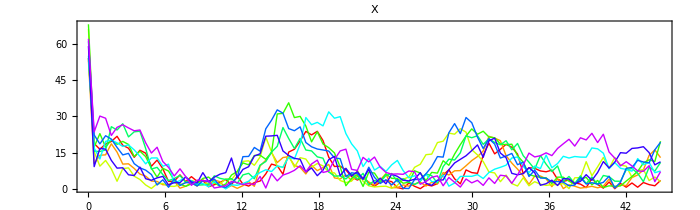

```mathematica
SimPlot[czsim, X, AspectRatio-> .3, ImageSize-> 700]
```

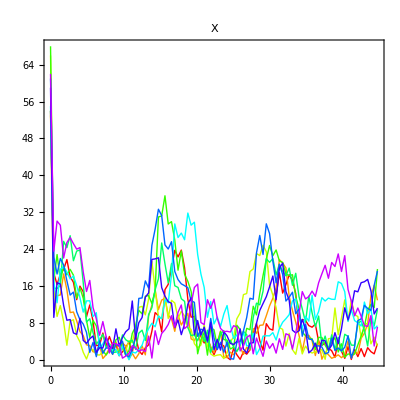
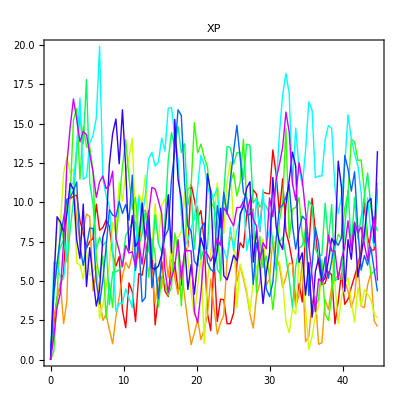
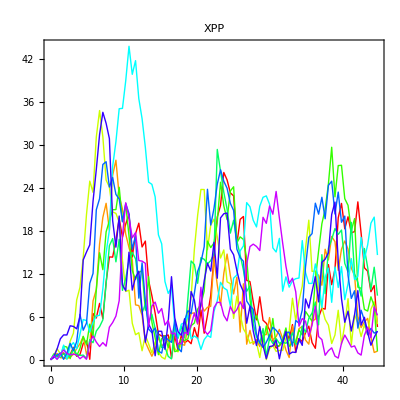
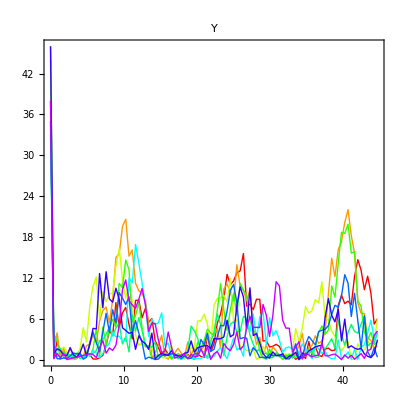
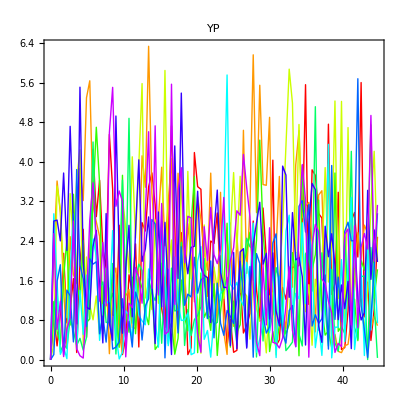
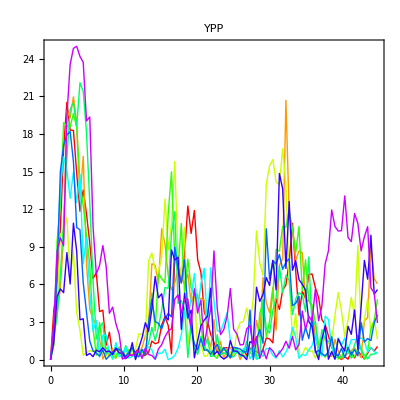
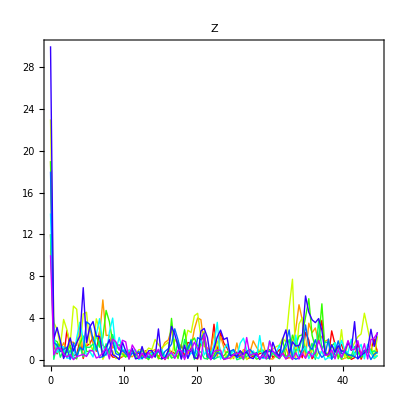
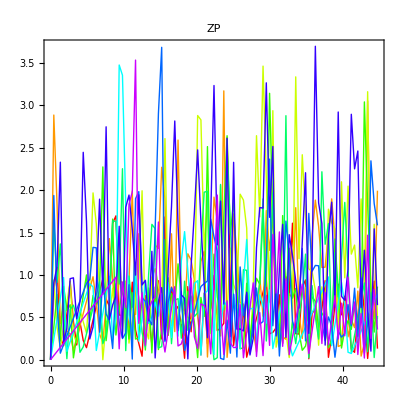

```mathematica
SimPlot[czsim]
```